# Nested sampling with the BayesianInference package

## General

Load the package:

```mathematica
SetDirectory[NotebookDirectory[]];
<<BayesianInference`
```

The general workflow for using this package is as follows:

Define an inference problem using defineInferenceProblem. This returns an inferenceObject that contains all of the relevant  information needed for the next steps. defineInferenceProblem will do some sanity checks to try and anticipate problems further ahead

Use nestedSampling or parallelNestedSampling to run the algorithm on the inferenceObject

Use visualisation functions to interpret the result

### defineInferenceProblem and inferenceObject

Here’s a typical usage example of defineInferenceProblem corresponding to the problem of inferencing the parameters of a normal distribution:

```mathematica
obj=defineInferenceProblem[
"Data"-> RandomVariate[NormalDistribution[0,1],100],
"GeneratingDistribution" -> NormalDistribution[mu, sigma],
"Parameters"->{{mu,-∞,∞},{sigma,0,∞}},
"PriorDistribution"-> ProductDistribution[NormalDistribution[0,100],ExponentialDistribution[1/100]]
]
```

inferenceObject[<< 7 defined properties >>]

Note the tooltip on the inferenceObject that gives a summary of its contents. The inferenceObject is basically just a wrapper for an Association that holds all relevant information. It’s important to note, though, that due to its typesetting you cannot copy-paste it in a notebook:

```mathematica
inferenceObject["<< \!\(\*RowBox[{\"7\"}]\) defined properties >>"]//FullForm
```

inferenceObject[Tooltip[Framed[StringForm["<< `1` defined properties >>",7]],Grid[List[List["Data","List (100 \[Times] 1)"],List["GeneratingDistribution","Distribution (1D, Real)"],List["Parameters","List (2 \[Times] 3)"],List["PriorDistribution","Distribution (2D, Vector)"],List["ParameterSymbols","List (2)"],List["LogLikelihoodFunction","CompiledFunction[...]"],List["LogPriorPDFFunction","CompiledFunction[...]"]],Rule[Alignment,Left],Rule[ItemSize,List[Automatic,Automatic]]]]]

This is intentional: if it was possible to copy-paste the object, it would be necessary to store potentially large amounts of data in the notebook, which would be slow.

This is how you check what properties are contained in the object:

```mathematica
obj["Properties"]
```

{Data,GeneratingDistribution,LogLikelihoodFunction,LogPriorPDFFunction,Parameters,ParameterSymbols,PriorDistribution,Properties}

You can add information manually, even properties that are just for your own convenience:

```mathematica
obj = Append[obj, "Name"-> "Example"]
obj["Properties"]
```

inferenceObject[<< 8 defined properties >>]

{Data,GeneratingDistribution,LogLikelihoodFunction,LogPriorPDFFunction,Name,Parameters,ParameterSymbols,PriorDistribution,Properties}

To see what possible inputs there are for defining your problem, evaluate:

```mathematica
defineInferenceProblem[]
```

{Data,Parameters,LogLikelihoodFunction,LogPriorPDFFunction,GeneratingDistribution,PriorDistribution,PriorPDF}

To run the nested sampling algorithm, we ultimately need to define the following properties:

Parameters: A list specifying the parameters that are to be estimated and their limits (which are allowed to be infinite)

LogLikelihoodFunction: a function (preferably compiled) that evaluates the loglikelihood at a given point in the parameter space

LogPriorPDFFunction: The logPDF function (preferably compiled) of the prior distribution (does not need to be normalised, but the computed evidence depends on its normalisation constant)

StartingPoints: A set of samples from the prior to use as a starting point

The role of defineInferenceProblem is to construct these properties from the properties supplied by the user. However, the you can forego the use of defineInferenceProblem by simply creating an association with the 4 required items and wrapping inferenceObject around it.

The convention that is used throughout this package, is that the n estimation parameters from an vector in nD space. For example, if the loglikelihood function is a function of 2 parameters, it should be of the form:

```mathematica
logLikelihood[paramVector_List]:= numericFunctionOf[paramVector[[1]],paramVector[[2]]];
```

```mathematica
$MachineLogZero
```

-1.77972×10^308

Furthermore, the code works best if we stay within the realm of machine numbers. However, since the log of zero cannot be represented in machine numbers, the package uses a value called $MachineLogZero instead:

```mathematica
$MachineLogZero
```

-1.77972×10^308

This value should be returned whenever the point in parameter space is outside of the support of the prior or loglikelihood. If you use defineInferenceProblem to create the loglikelihood and log prior PDF, this is handled automatically:

```mathematica
obj["LogPriorPDFFunction"][{0,1}]
obj["LogPriorPDFFunction"][{0,-1}]
obj["LogLikelihoodFunction"][{0,-1}]
```

-10.1393

-1.77972×10^308

-1.77972×10^308

#### Known issues:

Please note that if you specify an explicit PriorDistribution, the limits specified by the parameters will cut off the prior without adjusting the normalisation constant of the prior PDF:

```mathematica
Table[
With[{
obj=defineInferenceProblem[
"Data"-> RandomVariate[NormalDistribution[0,1],100],
"GeneratingDistribution" -> NormalDistribution[mu, sigma],
"Parameters"->{{mu,-lim,lim},{sigma,0,lim}},
"PriorDistribution"-> ProductDistribution[NormalDistribution[0,100],ExponentialDistribution[1/100]]
]
},
Quiet@NIntegrate[
Exp@obj["LogPriorPDFFunction"][{x,y}],
{x,-∞,∞},
{y,0,∞}
]
],
{lim, {∞,10}}
]
```

{1.,0.00758024}

When specifying the prior distribution as a list of distributions (in which case defineInferenceProblem will construct a ProductDistribution for you), the normalisation will be restored:

```mathematica
Table[
With[{
obj=defineInferenceProblem[
"Data"-> RandomVariate[NormalDistribution[0,1],100],
"GeneratingDistribution" -> NormalDistribution[mu, sigma],
"Parameters"->{{mu,-lim,lim},{sigma,0,lim}},
"PriorDistribution"-> {NormalDistribution[0,100],ExponentialDistribution[1/100]}
]
},
Quiet@NIntegrate[
Exp@obj["LogPriorPDFFunction"][{x,y}],
{x,-∞,∞},
{y,0,∞}
]
],
{lim, {∞,10}}
]
```

{1.,1.}

### General nested sampling problems

#### Cauchy distribution

```mathematica
dist=CauchyDistribution[0,1];
testdata=RandomVariate[dist,10];
```

```mathematica
obj =defineInferenceProblem[
"Data"-> testdata,
"GeneratingDistribution" -> CauchyDistribution[a, b],
"Parameters"->{{a,-100,100},{b,0.01,100}},
"PriorDistribution"-> {"LocationParameter", "ScaleParameter"},
"OriginalDistribution" -> dist
]
```

inferenceObject[<< 8 defined properties >>]

```mathematica
obj=generateStartingPoints[obj, 25]
```

inferenceObject[<< 9 defined properties >>]

```mathematica
result =parallelNestedSampling[
obj,
"MonteCarloSteps"->300,
"TerminationFraction" -> 0.001
]
result["LogEvidence"]
```

inferenceObject[<< 22 defined properties >>]

<|Mean→-22.3907,StandardError→0.228403|>

```mathematica
calculationReport[result]
```

```mathematica
result["Properties"]
```

{CrudeLogEvidence,CrudeRelativeEntropy,Data,EmpiricalPosteriorDistribution,GeneratedNestedSamples,GeneratingDistribution,LogEstimatedMissingEvidence,LogEvidence,LogLikelihoodFunction,LogLikelihoodMaximum,LogPriorPDFFunction,ParameterExpectedValues,ParameterRanges,Parameters,ParameterSymbols,PriorDistribution,Properties,RelativeEntropy,SamplePoolSize,Samples,StartingPoints,TotalSamples}

{-0.341054,0.661534}

{{0.116792,-0.00472128},{-0.00472128,0.0887529}}

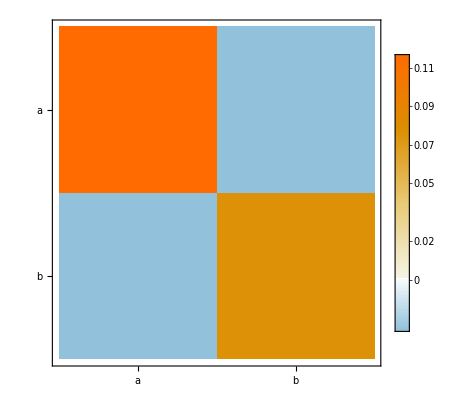

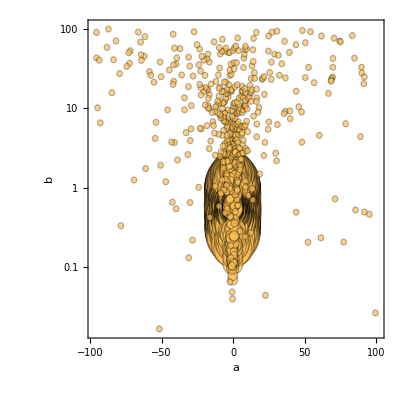

```mathematica
Mean[result["EmpiricalPosteriorDistribution"]]
Covariance[result["EmpiricalPosteriorDistribution"]]
covarianceMatrixPlot[result]
posteriorBubbleChart[result,{a,b},
ScalingFunctions->{None,"Log",None},
PerformanceGoal-> "Speed"
]
```

```mathematica
posteriorBubbleChart[
takePosteriorFraction[result,0.99],{1,2},
ScalingFunctions->{None,"Log",None}
]
```

-Graphics-

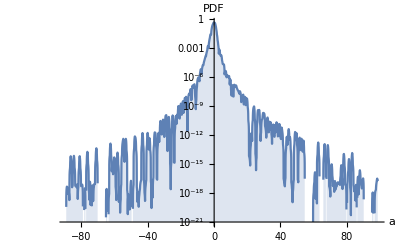

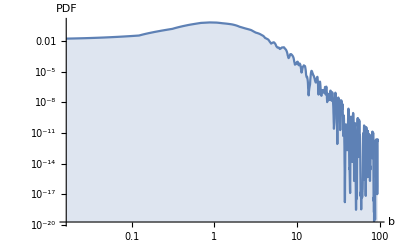

```mathematica
posteriorMarginalPDFPlot1D[result,a,ScalingFunctions->"Log"]
posteriorMarginalPDFPlot1D[result,b,ScalingFunctions->{"Log","Log"}]
```

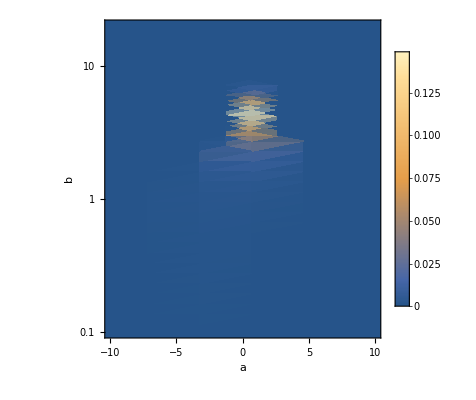

```mathematica
posteriorMarginalPDFDensityPlot2D[result,{a,b},ScalingFunctions->{None, "Log",None},PlotPoints->50,PlotRange->{{-10,10},{0.1,20},All}]
```

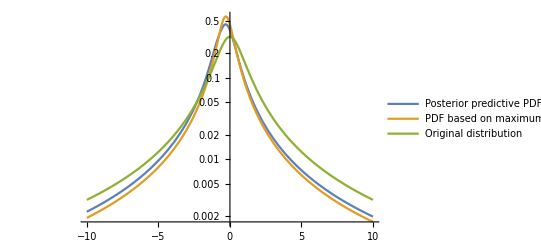

```mathematica
LogPlot[
Evaluate[{
PDF[predictiveDistribution[result],x],
PDF[EstimatedDistribution[Flatten @ result["Data"],result["GeneratingDistribution"],ParameterEstimator->{"MaximumLikelihood", Method -> "FindMaximum"}], x],
PDF[result["OriginalDistribution"],x]
}],
{x,-10,10},
PlotRange->All,
PlotLegends->{"Posterior predictive PDF", "PDF based on maximum likelihood estimate", "Original distribution"}
]
```

```mathematica
obj2 =defineInferenceProblem[
"Data"-> testdata,
"GeneratingDistribution" -> NormalDistribution[a, b],
"Parameters"->{{a,-100,100},{b,0.01,100}},
"PriorDistribution"-> {"LocationParameter", "ScaleParameter"}
];
obj2=generateStartingPoints[obj2, 25];
result2 =parallelNestedSampling[
obj2,
"MonteCarloSteps"->300,
"TerminationFraction" -> 0.001
]
result2["LogEvidence"]
```

inferenceObject[<< 21 defined properties >>]

<|Mean→-41.0492,StandardError→0.203716|>

```mathematica
posteriorMarginalPDFPlot1D[result,a,ScalingFunctions->"Log"]
posteriorMarginalPDFPlot1D[result,b,ScalingFunctions->{"Log","Log"}]
```

-Graphics-

-Graphics-

#### Fitting Normal data with a SkewNormal distribution

```mathematica
dist=NormalDistribution[0,1];
testdata=RandomVariate[dist,20];
result=<||>;
```

```mathematica
dist=SkewNormalDistribution[0,1,1];
testdata=RandomVariate[dist,20];
result=<||>;
```

```mathematica
Plot[
Evaluate[{
PDF[NormalDistribution[0,1],x],
PDF[SkewNormalDistribution[0,1,1],x]
}],
{x,-3,3},
Filling->Axis
]
```

```mathematica
With[{vars={
{loc,-20,20},
{scale,0.01,100}
}
},
result["Normal"] = nestedSampling[
LogLikelihood[NormalDistribution[##],testdata]&,
{"LocationParameter", "ScaleParameter"},
vars
]
];
With[{vars={
{loc,-20,20},
{scale,0.01,100},
{scew, -20,20}
}
},
result["SkewNormal"] = nestedSampling[
LogLikelihood[SkewNormalDistribution[##],testdata]&,
{"LocationParameter", "ScaleParameter","LocationParameter"},
vars
]
];
Dataset[result[[All,"LogEvidence"]]]
```

```mathematica
posteriorBubbleChart[result[["Normal"]],{1,2},0.99]
posteriorBubbleChart[result[["SkewNormal"]],{1,2},0.99]
posteriorBubbleChart[result[["SkewNormal"]],{1,2,3},0.99]
```

```mathematica
Show[
Histogram[testdata,Length[testdata],"PDF"],
Plot[
Evaluate[{
PDF[predictiveDistribution[result[["Normal"]],NormalDistribution,0.99],x],
PDF[predictiveDistribution[result[["SkewNormal"]],SkewNormalDistribution,0.99],x]
}],
{x,-4,4},
PlotRange->All,
Filling->Axis
],
PlotRange->All
]
```

#### Regression

```mathematica
BlockRandom[
SeedRandom[1];
testdata={#,(#+2 RandomReal[])}&/@RandomReal[{-1,1},20];
ListPlot[testdata]
]
vars[order_]:={
Sequence@@Table[{Symbol["c"<>ToString[i]],-100,100},{i,0,order}],
{s0,0.01,100}
};
```

```mathematica
result=
Association@Table[
order-> With[{
logLikelihood=
BayesianUtilities`Private`regressionLogLikelihoodFunction[
Rule @@ Transpose[testdata],
Most[vars[order]][[All,1]].x^Range[0,order],
 NormalDistribution[0,s0],
{x},
vars[order][[All,1]]
],
prior= Flatten@{ConstantArray["LocationParameter",order+1], "ScaleParameter"}
},
nestedSampling[
logLikelihood,
prior,
vars[order],
"MonteCarloSteps"->300,
"SamplePoolSize"->100,
"MaxIterations"->3000
]
],
{order,{1,2}}];
Dataset[result[[All,{"LogEvidence"}]]]
```

```mathematica
With[{order = 1},
Module[{points=Values[Values/@takePosteriorFraction[result[order],0.9][["Samples",All, {"Point","CrudePosteriorWeight"}]]]},
points=MapAt[
#/points[[1,2]]&,
points,
{All,2}
];
points=Map[
Style[Most[#[[1]]].x^Range[0,order],Opacity[#[[2]]]]&,
points
];
Plot[Evaluate[points],{x,-2.5,2.5},PlotStyle->Black, Epilog->{Red,PointSize[0.01],Point[testdata]}]
]
]
```

```mathematica
Column@Table[
With[{dist=Function[Evaluate[vars[order][[All,1]]],
Evaluate@TransformedDistribution[Most[vars[order]][[All,1]].#^Range[0,order]+e,e\[Distributed]NormalDistribution[0,vars[order][[-1,1]]]]
],
xvalues = Range[-2.5,2.5,0.25]
},
Show[
ListPlot[
Transpose[
Function[
InverseCDF[
predictiveDistribution[
result[order],
dist
,
0.99
],
{0.01,0.5,0.99}
]
]/@xvalues
],
Joined->True,
DataRange->MinMax[xvalues],
ImageSize->500,
PlotLabels->Placed[{"1%", "median", "99%"},{Scaled[1],Above}]
],
Graphics[{Red,PointSize[0.01],Point[testdata]}]
]
],
{order,Keys[result]}
]
```

#### Stochastic DEs

### Gaussian process

#### 1D

```mathematica
testdata=With[
{x=RandomReal[{0,10},100]},
x->
Function[
Sin[0.5 #]+0.4Sin[2 #]+0.4#+1+0.3*RandomVariate[NormalDistribution[],Length[x]]
][x+0.2*RandomVariate[NormalDistribution[],Length[x]]
]
];
ListPlot[List@@@Thread[testdata]]
```

```mathematica
result=
With[{vars={
{s1,0.01,100},
{l,0.05, 30},
{s0,0.02,20},
{m, -10,10}
}
},
gaussianProcessNestedSampling[
normalizeData[testdata],
Function[s1 *Boole[Subtract[#1,#2]^2<(6 l)^2] Exp[-Divide[Subtract[#1,#2]^2,l^2]]],
Function[s0],
Function[m],
{"ScaleParameter", "ScaleParameter","ScaleParameter", "LocationParameter"},
vars,
"SamplePoolSize" -> 25,
"MaxIterations"->10000,
"MinIterations"->20,
"MonteCarloSteps"->100,
"MonteCarloStepDistribution" ->NormalDistribution,
"InitialMonteCarloStepSize" -> 0.075,
"TerminationFraction" -> 0.01,
"Monitor" -> True,
"Likelihood" -> "Custom",
"LikelihoodMaximum"->Automatic,
"MonteCarloStepSizeAdjustment" -> {"Order" -> 2, "HistoryLength"->10},
"ParallelRuns"->4
]
];
Dataset[result]
```

```mathematica
covarianceMatrixPlot[result]
```

```mathematica
posteriorMarginalPDFPlot1D[result,1]
```

```mathematica
posteriorMarginalPDFDensityPlot2D[result,{1,2}]
```

```mathematica
posteriorBubbleChart[result,{1,2,3},0.99]
```

```mathematica
predictions = predictFromGaussianProcess[result, Range[-3,3,0.2],0.99];
gaussianProcessPredictionPlot[result, predictions, "DistributionPercentiles" -> {0.01, 0.5, 0.99}]
```

```mathematica
calculationReport[result]
```

#### Polynomial fitting

```mathematica
testdata=With[
{x=RandomReal[{0,10},20]},
x->
Function[
0.4#+1+1*RandomVariate[CauchyDistribution[],Length[x]]
][x]
];
result=<||>;
ListPlot[List@@@Thread[testdata]]
```

```mathematica
result=
Association@Table[
order-> With[{vars={
Sequence@@Table[{Symbol["x"<>ToString[i]],-100,100},{i,0,order}],
{s0,0.01,100}
}
},
gaussianProcessNestedSampling[
normalizeData[testdata],
Function[0],
Function[s0],
Function[Evaluate[Total@Table[vars[[i,1]] #^(i-1),{i,1,Length[vars]-1}]]],
Flatten@{ConstantArray["LocationParameter",Length[vars]-1], "ScaleParameter"},
vars,
"Likelihood" -> "Custom",
"MonteCarloSteps"->300
]
],
{order,{2,3,4}}];
Dataset[result[[All,"LogEvidence"]]]
```

```mathematica
Column[Table[
posteriorBubbleChart[result[[i]], {1,2,-1},0.99],
{i,Length[result]}
]]
```

```mathematica
predictions = predictFromGaussianProcess[#, Range[-3,3,0.2],0.99]&/@result;
Column[Table[
gaussianProcessPredictionPlot[result[[i]], predictions[[i]], "DistributionPercentiles" -> {0.01,0.5,0.99}],
{i,Length[result]}
]]
```

#### With trend in noise level

```mathematica
result=
Association@Table[
order-> With[{vars={
Sequence@@Table[{Symbol["x"<>ToString[i]],-100,100},{i,0,order}],
{s0,0.01,100},
{s1,0.01,100}
}
},
gaussianProcessNestedSampling[
normalizeData[testdata],
Function[0],
Function[(s0 + # s1)^2],
Function[Evaluate[Total@Table[vars[[i,1]] #^(i-1),{i,1,Length[vars]-2}]]],
Flatten@{ConstantArray["LocationParameter",Length[vars]-1], "ScaleParameter"},
vars,
"Likelihood" -> Automatic,
"MonteCarloSteps"->300
]
],
{order,{1}}];
Dataset[result[[All,"LogEvidence"]]]
```

```mathematica
predictions = predictFromGaussianProcess[#, Range[-3,3,0.2],0.99]&/@result;
Column[Table[
gaussianProcessPredictionPlot[result[[i]], predictions[[i]], "DistributionPercentiles" -> {0.01,0.5,0.99}],
{i,Length[result]}
]]
```

#### 2D

```mathematica
testdata=#->((#[[All,1]])^2-(#[[All,2]])^2)& @ RandomReal[{-1,1},{100,2}];
ListPlot3D[Transpose@Join[Transpose@testdata[[1]],{testdata[[2]]}]]
```

```mathematica
result=
With[{vars={
{s1,0.01,100},
{l,0.05, 30},
{s0,0.02,20},
{m, -10,10}
}
},
gaussianProcessNestedSampling[
normalizeData[testdata],
Function[
With[{dist = Norm[Subtract[#1,#2]]},
s1 *Boole[dist<(6 l)^2] Exp[-Divide[dist,l]^2]
]
],
Function[s0],
Function[m],
{"ScaleParameter", "ScaleParameter","ScaleParameter", "LocationParameter"},
vars,
"SamplePoolSize" -> 25,
"MaxIterations"->10000,
"MinIterations"->20,
"MonteCarloSteps"->100,
"InitialMonteCarloStepSize" -> 0.075,
"TerminationFraction" -> 0.01,
"Monitor" -> True,
"Likelihood" -> "Custom",
"LikelihoodMaximum"->Automatic,
"MonteCarloStepSizeAdjustment" -> {"Order" -> 2, "HistoryLength"->10}
]
];
Dataset[result]
```

```mathematica
predictFromGaussianProcess[result, 10,1]
```

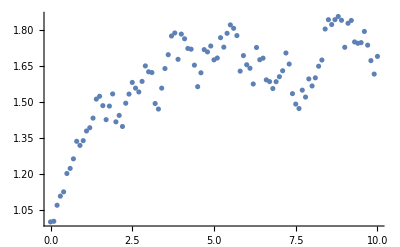

```mathematica
testData=Normal@RandomFunction[OrnsteinUhlenbeckProcess[2,.2,.3,1],{0,10,.1}];
ListPlot@testData
```

```mathematica
resultOUP=parallelNestedSampling[
With[{dat=testData},
Function[{μ,σ,θ},LogLikelihood[OrnsteinUhlenbeckProcess[μ,σ,θ,dat[[1,1,2]]],Rest/@dat]]
],
{"LocationParameter","ScaleParameter","ScaleParameter"},
{
{μ,-10,10},
{σ,0.01,20},
{θ,0.01,20}
},
"MonteCarloSteps"->300,
"SamplePoolSize"->25,
"MaxIterations"->1000,
"ParallelRuns"->4
];
Dataset[resultOUP]
```

```mathematica
resultOUP["LogEvidence"]
```

<|Mean→134.523,StandardError→0.228609|>

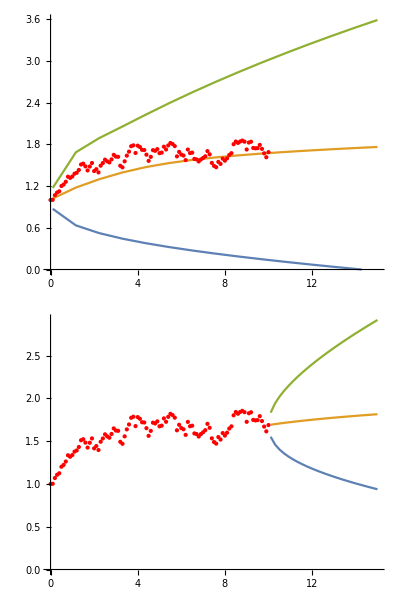

```mathematica
With[{max =15},
Column[{
Show[
ListPlot[
Transpose@Table[
InverseCDF[
predictiveDistribution[
resultOUP,
OrnsteinUhlenbeckProcess[##,testData[[1,1,2]]][t]&,
0.99
],
{0.01,0.5,0.99}
],
{t,0.1,max,1}
],
DataRange->{0.1,max},
ImageSize->500,
Joined->True,
PlotRange->{{0,max},{0,All}}
],
Graphics[{Red,Point/@testData}]
],
Show[
ListPlot[
Transpose@Table[
InverseCDF[
predictiveDistribution[
resultOUP,
OrnsteinUhlenbeckProcess[##,testData[[1,-1,2]]][t]&,
0.99
],
{0.01,0.5,0.99}
],
{t,0.1,max-10,0.2}
],
DataRange->{10.1,max},
ImageSize->500,
Joined->True,
PlotRange->{{0,max},{0,All}}
],
Graphics[{Red,Point/@testData}]
]
}]
]
```

```mathematica
resultGBM=parallelNestedSampling[
With[{dat=testData},
Function[{μ,σ},LogLikelihood[GeometricBrownianMotionProcess[μ,σ,dat[[1,1,2]]],Rest/@dat]]
],
{"ScaleParameter","ScaleParameter"},
{
{μ,0.01,100},
{σ,0.01,20}
},
"MonteCarloSteps"->300,
"SamplePoolSize"->25,
"MaxIterations"->1000,
"ParallelRuns"->4
];
Dataset[resultGBM]
```

```mathematica
resultGBM["LogEvidence"]
```

<|Mean→134.549,StandardError→0.235583|>

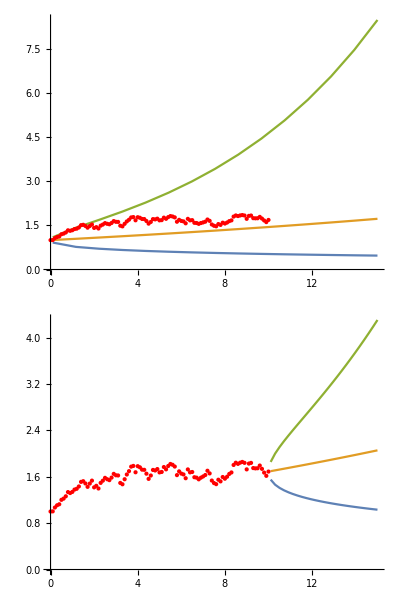

```mathematica
With[{max =15},
Column[{
Show[
ListPlot[
Transpose@Table[
InverseCDF[
predictiveDistribution[
resultGBM,
GeometricBrownianMotionProcess[##,testData[[1,1,2]]][t]&,
0.99
],
{0.01,0.5,0.99}
],
{t,0.1,max,1}
],
DataRange->{0.1,max},
ImageSize->500,
Joined->True,
PlotRange->{{0,max},{0,All}}
],
Graphics[{Red,Point/@testData}]
],
Show[
ListPlot[
Transpose@Table[
InverseCDF[
predictiveDistribution[
resultGBM,
GeometricBrownianMotionProcess[##,testData[[1,-1,2]]][t]&,
0.99
],
{0.01,0.5,0.99}
],
{t,0.1,max-10,0.2}
],
DataRange->{10.1,max},
ImageSize->500,
Joined->True,
PlotRange->{{0,max},{0,All}}
],
Graphics[{Red,Point/@testData}]
]
}]
]
```